```mathematica
p=Subdivide[0.05,5,29]
```

{0.05,0.22069,0.391379,0.562069,0.732759,0.903448,1.07414,1.24483,1.41552,1.58621,1.7569,1.92759,2.09828,2.26897,2.43966,2.61034,2.78103,2.95172,3.12241,3.2931,3.46379,3.63448,3.80517,3.97586,4.14655,4.31724,4.48793,4.65862,4.82931,5.}

```mathematica
p[[8;;]]
```

{1.24483,1.41552,1.58621,1.7569,1.92759,2.09828,2.26897,2.43966,2.61034,2.78103,2.95172,3.12241,3.2931,3.46379,3.63448,3.80517,3.97586,4.14655,4.31724,4.48793,4.65862,4.82931,5.}

```mathematica
p[[;;4]]
```

{0.05,0.22069,0.391379,0.562069}

```mathematica
Tuples[{p[[;;4]],p[[8;;]]}]//Length
```

92

```mathematica
Select[Round[meanrtilde,10.^-3],#[[1]]==0.562&&0.46>=#[[3]]&]
```

{{0.562,0.05,0.38},{0.562,0.221,0.398}}

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

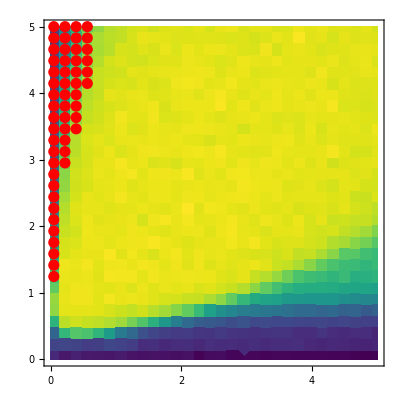

```mathematica
fontSize=32;
fig=
ListDensityPlot[meanrtilde,
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),
ColorFunctionScaling->True,
PlotRange->{{0.0,5.0},{0.0,5.0}},
PlotRangePadding->0.0,
Frame->True,
FrameStyle->Directive[FontFamily->"Latin Modern Math",FontSize->fontSize,Black,Thick],
FrameTicks->{
{#1,#2},
{#1,#2}
}&[Join[Table[{i,i,0.03,Directive[Black,Thick]},{i,0,5}],Table[{i,None,0.03,Directive[Black,Thick]},{i,0.5,4.5}],Table[{i,None,0.015,Directive[Black,Thick]},{i,0.1,4.9,0.1}]],Join[Table[{i,None,0.03,Directive[Black,Thick]},{i,0,5}],Table[{i,None,0.03,Directive[Black,Thick]},{i,0.5,4.5}],Table[{i,None,0.015,Directive[Black,Thick]},{i,0.1,4.9,0.1}]]],
FrameTicksStyle->Directive[Black],
AspectRatio->1,
Epilog->{Red,PointSize[0.02],Point[#]&/@Catenate[Table[{p[[i]],p[[j]]},{i,4,1,-1},{j,30,f[i],-1}]]}
]
```

```mathematica
9*3600
```

32400

```mathematica
22*40+75
```

955

```mathematica
{x,y}={2,26};
{ArrayReshape[meanrtilde,{30,30,3}][[x,y]],ArrayReshape[meanrtilde6,{30,30,3}][[x,y]],ArrayReshape[meanrtilde5,{30,30,3}][[x,y]]}
```

{{0.22069,4.31724,0.459769},{0.22069,4.31724,0.448273},{0.22069,4.31724,0.431207}}

```mathematica
Fit[{{5,0.43120696608893305},{6,0.44827324946482283},{7,0.45976865586677773}},{1,t},t]/.t->8
```

0.474978

```mathematica
f[1]:=8
f[2]:=16
f[3]:=20
f[4]:=25
Catenate[Table[{p[[i]],p[[j]]},{i,4,1,-1},{j,30,f[i],-1}]]//Length
```

55

```mathematica
Catenate[Table[{p[[i]],p[[j]]},{i,4,1,-1},{j,30,f[i],-1}]][[;;23]]
```

{{0.562069,5.},{0.562069,4.82931},{0.562069,4.65862},{0.562069,4.48793},{0.562069,4.31724},{0.562069,4.14655},{0.562069,3.97586},{0.391379,5.},{0.391379,4.82931},{0.391379,4.65862},{0.391379,4.48793},{0.391379,4.31724},{0.391379,4.14655},{0.391379,3.97586},{0.391379,3.80517},{0.391379,3.63448},{0.391379,3.46379},{0.391379,3.2931},{0.22069,5.},{0.22069,4.82931},{0.22069,4.65862},{0.22069,4.48793},{0.22069,4.31724}}

```mathematica
DatePlus[Now,Quantity[17*2,"Hours"]]
```

Sat 17 May 2025 02:31:51GMT-6

```mathematica
>
```

```mathematica
f[1]:=8
f[2]:=16
f[3]:=22
f[4]:=25
```

```mathematica
meanrtilde6=
Table[
Module[
{ε=i[[1]],
Jxy=i[[2]],
eigenenergies},
eigenenergies=Flatten[Import["data/eigenenergies/xxz/L_18/k_6/Jz_1_omega_0_d_9_epsilon_"<>ToString[NumberForm[ε,{Infinity,2}]]<>"_Jxy_"<>ToString[NumberForm[Jxy,{Infinity,2}]]<>".csv"]];
{ε,Jxy,MeanLevelSpacingRatio[Sort[Chop[eigenenergies]]]}
]
,{i,parameters}];
```

Divide::infy: Infinite expression (4.9738×10^-14)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

```mathematica
meanrtilde5=
Table[
Module[
{ε=i[[1]],
Jxy=i[[2]],
eigenenergies},
eigenenergies=Flatten[Import["data/eigenenergies/xxz/L_18/k_5/Jz_1_omega_0_d_9_epsilon_"<>ToString[NumberForm[ε,{Infinity,2}]]<>"_Jxy_"<>ToString[NumberForm[Jxy,{Infinity,2}]]<>".csv"]];
{ε,Jxy,MeanLevelSpacingRatio[Sort[Chop[eigenenergies]]]}
]
,{i,parameters}]
```

Divide::infy: Infinite expression 0.49875/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Import::nffil: File data/eigenenergies/xxz/L_18/k_5/Jz_1_omega_0_d_9_epsilon_1.59_Jxy_0.39.csv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File data/eigenenergies/xxz/L_18/k_5/Jz_1_omega_0_d_9_epsilon_1.93_Jxy_3.63.csv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Divide::infy: Infinite expression (6.39516×10^-10)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

{{0.05,0.05,0.417749},{0.05,0.22069,0.419717},{0.05,0.391379,0.42477},{0.05,0.562069,0.451979},{0.05,0.732759,0.47247},{0.05,0.903448,0.476327},{0.05,1.07414,0.461083},{0.05,1.24483,0.449304},{0.05,1.41552,0.441373},{0.05,1.58621,0.43569},{0.05,1.7569,0.431494},{0.05,1.92759,0.433148},{0.05,2.09828,0.424799},{0.05,2.26897,0.417419},{0.05,2.43966,0.422279},{0.05,2.61034,0.417499},{0.05,2.78103,0.416958},{0.05,2.95172,0.416714},{0.05,3.12241,0.409842},{0.05,3.2931,0.410068},{0.05,3.46379,0.403228},{0.05,3.63448,0.401487},{0.05,3.80517,0.407805},{0.05,3.97586,0.403618},{0.05,4.14655,0.403386},{0.05,4.31724,0.401397},{0.05,4.48793,0.404484},{0.05,4.65862,0.40607},{0.05,4.82931,0.395518},{0.05,5.,0.393039},{0.22069,0.05,0.392699},{0.22069,0.22069,0.419777},{0.22069,0.391379,0.444566},{0.22069,0.562069,0.497765},{0.22069,0.732759,0.516884},{0.22069,0.903448,0.524326},{0.22069,1.07414,0.529552},{0.22069,1.24483,0.526229},{0.22069,1.41552,0.518325},{0.22069,1.58621,0.511907},{0.22069,1.7569,0.509768},{0.22069,1.92759,0.499591},{0.22069,2.09828,0.494709},{0.22069,2.26897,0.489946},{0.22069,2.43966,0.482003},{0.22069,2.61034,0.472705},{0.22069,2.78103,0.466341},{0.22069,2.95172,0.462058},{0.22069,3.12241,0.462811},{0.22069,3.2931,0.452904},{0.22069,3.46379,0.450825},{0.22069,3.63448,0.443664},{0.22069,3.80517,0.438685},{0.22069,3.97586,0.437385},{0.22069,4.14655,0.437157},{0.22069,4.31724,0.431207},{0.22069,4.48793,0.431956},{0.22069,4.65862,0.422438},{0.22069,4.82931,0.421191},{0.22069,5.,0.42542},{0.391379,0.05,0.386094},{0.391379,0.22069,0.407822},{0.391379,0.391379,0.454786},{0.391379,0.562069,0.503975},{0.391379,0.732759,0.519232},{0.391379,0.903448,0.526139},{0.391379,1.07414,0.531355},{0.391379,1.24483,0.527262},{0.391379,1.41552,0.53317},{0.391379,1.58621,0.522556},{0.391379,1.7569,0.520847},{0.391379,1.92759,0.523865},{0.391379,2.09828,0.52184},{0.391379,2.26897,0.513138},{0.391379,2.43966,0.50451},{0.391379,2.61034,0.504115},{0.391379,2.78103,0.507439},{0.391379,2.95172,0.491053},{0.391379,3.12241,0.489229},{0.391379,3.2931,0.488286},{0.391379,3.46379,0.47029},{0.391379,3.63448,0.478865},{0.391379,3.80517,0.469127},{0.391379,3.97586,0.469014},{0.391379,4.14655,0.463428},{0.391379,4.31724,0.458252},{0.391379,4.48793,0.446222},{0.391379,4.65862,0.447013},{0.391379,4.82931,0.442707},{0.391379,5.,0.44427},{0.562069,0.05,0.388529},{0.562069,0.22069,0.40538},{0.562069,0.391379,0.443508},{0.562069,0.562069,0.505703},{0.562069,0.732759,0.522397},{0.562069,0.903448,0.528111},{0.562069,1.07414,0.533879},{0.562069,1.24483,0.52649},{0.562069,1.41552,0.527856},{0.562069,1.58621,0.529108},{0.562069,1.7569,0.528118},{0.562069,1.92759,0.524696},{0.562069,2.09828,0.527543},{0.562069,2.26897,0.521721},{0.562069,2.43966,0.518685},{0.562069,2.61034,0.515868},{0.562069,2.78103,0.518232},{0.562069,2.95172,0.511892},{0.562069,3.12241,0.50801},{0.562069,3.2931,0.500812},{0.562069,3.46379,0.497175},{0.562069,3.63448,0.487173},{0.562069,3.80517,0.489194},{0.562069,3.97586,0.486363},{0.562069,4.14655,0.488115},{0.562069,4.31724,0.469908},{0.562069,4.48793,0.469943},{0.562069,4.65862,0.467458},{0.562069,4.82931,0.462263},{0.562069,5.,0.455028},{0.732759,0.05,0.389758},{0.732759,0.22069,0.407202},{0.732759,0.391379,0.437319},{0.732759,0.562069,0.497202},{0.732759,0.732759,0.522411},{0.732759,0.903448,0.532201},{0.732759,1.07414,0.530677},{0.732759,1.24483,0.531556},{0.732759,1.41552,0.527923},{0.732759,1.58621,0.524481},{0.732759,1.7569,0.52514},{0.732759,1.92759,0.526478},{0.732759,2.09828,0.52312},{0.732759,2.26897,0.523773},{0.732759,2.43966,0.519439},{0.732759,2.61034,0.521491},{0.732759,2.78103,0.521359},{0.732759,2.95172,0.513617},{0.732759,3.12241,0.516655},{0.732759,3.2931,0.51332},{0.732759,3.46379,0.514064},{0.732759,3.63448,0.500649},{0.732759,3.80517,0.499185},{0.732759,3.97586,0.501305},{0.732759,4.14655,0.498699},{0.732759,4.31724,0.484881},{0.732759,4.48793,0.486938},{0.732759,4.65862,0.482789},{0.732759,4.82931,0.476763},{0.732759,5.,0.4708},{0.903448,0.05,(3259.62+Min[0,ComplexInfinity]+Min[0.,ComplexInfinity])/8566},{0.903448,0.22069,0.408199},{0.903448,0.391379,0.439266},{0.903448,0.562069,0.492897},{0.903448,0.732759,0.523083},{0.903448,0.903448,0.530564},{0.903448,1.07414,0.526135},{0.903448,1.24483,0.522534},{0.903448,1.41552,0.53318},{0.903448,1.58621,0.52484},{0.903448,1.7569,0.531288},{0.903448,1.92759,0.524809},{0.903448,2.09828,0.530005},{0.903448,2.26897,0.52805},{0.903448,2.43966,0.528135},{0.903448,2.61034,0.523181},{0.903448,2.78103,0.526756},{0.903448,2.95172,0.522839},{0.903448,3.12241,0.519086},{0.903448,3.2931,0.522647},{0.903448,3.46379,0.511919},{0.903448,3.63448,0.509704},{0.903448,3.80517,0.509299},{0.903448,3.97586,0.51381},{0.903448,4.14655,0.505094},{0.903448,4.31724,0.506528},{0.903448,4.48793,0.497508},{0.903448,4.65862,0.495417},{0.903448,4.82931,0.485581},{0.903448,5.,0.484625},{1.07414,0.05,0.390112},{1.07414,0.22069,0.411476},{1.07414,0.391379,0.425462},{1.07414,0.562069,0.478853},{1.07414,0.732759,0.510146},{1.07414,0.903448,0.525637},{1.07414,1.07414,0.523166},{1.07414,1.24483,0.535071},{1.07414,1.41552,0.533454},{1.07414,1.58621,0.535374},{1.07414,1.7569,0.533951},{1.07414,1.92759,0.529157},{1.07414,2.09828,0.53425},{1.07414,2.26897,0.525578},{1.07414,2.43966,0.526008},{1.07414,2.61034,0.527931},{1.07414,2.78103,0.525007},{1.07414,2.95172,0.524188},{1.07414,3.12241,0.521679},{1.07414,3.2931,0.530406},{1.07414,3.46379,0.5225},{1.07414,3.63448,0.520022},{1.07414,3.80517,0.511383},{1.07414,3.97586,0.511807},{1.07414,4.14655,0.512286},{1.07414,4.31724,0.511977},{1.07414,4.48793,0.496856},{1.07414,4.65862,0.492774},{1.07414,4.82931,0.493651},{1.07414,5.,0.490793},{1.24483,0.05,0.382705},{1.24483,0.22069,0.40087},{1.24483,0.391379,0.418084},{1.24483,0.562069,0.47014},{1.24483,0.732759,0.502988},{1.24483,0.903448,0.522019},{1.24483,1.07414,0.525928},{1.24483,1.24483,0.532862},{1.24483,1.41552,0.53422},{1.24483,1.58621,0.525618},{1.24483,1.7569,0.526192},{1.24483,1.92759,0.536429},{1.24483,2.09828,0.529521},{1.24483,2.26897,0.522048},{1.24483,2.43966,0.523176},{1.24483,2.61034,0.528341},{1.24483,2.78103,0.524422},{1.24483,2.95172,0.529242},{1.24483,3.12241,0.523823},{1.24483,3.2931,0.519263},{1.24483,3.46379,0.521132},{1.24483,3.63448,0.526512},{1.24483,3.80517,0.523796},{1.24483,3.97586,0.518793},{1.24483,4.14655,0.513608},{1.24483,4.31724,0.516583},{1.24483,4.48793,0.506415},{1.24483,4.65862,0.504333},{1.24483,4.82931,0.495886},{1.24483,5.,0.496157},{1.41552,0.05,0.388308},{1.41552,0.22069,0.394331},{1.41552,0.391379,0.412701},{1.41552,0.562069,0.455881},{1.41552,0.732759,0.504641},{1.41552,0.903448,0.526609},{1.41552,1.07414,0.524856},{1.41552,1.24483,0.533636},{1.41552,1.41552,0.528492},{1.41552,1.58621,0.533705},{1.41552,1.7569,0.528552},{1.41552,1.92759,0.525252},{1.41552,2.09828,0.528163},{1.41552,2.26897,0.527289},{1.41552,2.43966,0.525348},{1.41552,2.61034,0.526713},{1.41552,2.78103,0.525511},{1.41552,2.95172,0.524507},{1.41552,3.12241,0.521262},{1.41552,3.2931,0.524382},{1.41552,3.46379,0.523484},{1.41552,3.63448,0.520428},{1.41552,3.80517,0.521121},{1.41552,3.97586,0.520332},{1.41552,4.14655,0.520009},{1.41552,4.31724,0.511634},{1.41552,4.48793,0.510596},{1.41552,4.65862,0.513826},{1.41552,4.82931,0.503973},{1.41552,5.,0.505904},{1.58621,0.05,0.386352},{1.58621,0.22069,0.394285},{1.58621,0.391379,1/2 (1/Ratios[Differences[Flatten[$Failed]]]+Ratios[Differences[Flatten[$Failed]]])},{1.58621,0.562069,0.44285},{1.58621,0.732759,0.493308},{1.58621,0.903448,0.518247},{1.58621,1.07414,0.525067},{1.58621,1.24483,0.533006},{1.58621,1.41552,0.525329},{1.58621,1.58621,0.524476},{1.58621,1.7569,0.526527},{1.58621,1.92759,0.529386},{1.58621,2.09828,0.528363},{1.58621,2.26897,0.524479},{1.58621,2.43966,0.526503},{1.58621,2.61034,0.527333},{1.58621,2.78103,0.52724},{1.58621,2.95172,0.525847},{1.58621,3.12241,0.520036},{1.58621,3.2931,0.51899},{1.58621,3.46379,0.526127},{1.58621,3.63448,0.521182},{1.58621,3.80517,0.517826},{1.58621,3.97586,0.52528},{1.58621,4.14655,0.521333},{1.58621,4.31724,0.520942},{1.58621,4.48793,0.518141},{1.58621,4.65862,0.512894},{1.58621,4.82931,0.515067},{1.58621,5.,0.504791},{1.7569,0.05,0.386457},{1.7569,0.22069,0.38979},{1.7569,0.391379,0.393865},{1.7569,0.562069,0.426427},{1.7569,0.732759,0.479661},{1.7569,0.903448,0.51364},{1.7569,1.07414,0.523545},{1.7569,1.24483,0.529841},{1.7569,1.41552,0.527786},{1.7569,1.58621,0.533796},{1.7569,1.7569,0.521908},{1.7569,1.92759,0.531882},{1.7569,2.09828,0.522786},{1.7569,2.26897,0.52298},{1.7569,2.43966,0.526526},{1.7569,2.61034,0.529881},{1.7569,2.78103,0.526464},{1.7569,2.95172,0.529142},{1.7569,3.12241,0.522573},{1.7569,3.2931,0.524858},{1.7569,3.46379,0.52846},{1.7569,3.63448,0.522463},{1.7569,3.80517,0.522798},{1.7569,3.97586,0.523531},{1.7569,4.14655,0.519215},{1.7569,4.31724,0.522011},{1.7569,4.48793,0.519655},{1.7569,4.65862,0.514081},{1.7569,4.82931,0.51471},{1.7569,5.,0.509963},{1.92759,0.05,0.3845},{1.92759,0.22069,0.392169},{1.92759,0.391379,0.398219},{1.92759,0.562069,0.420674},{1.92759,0.732759,0.470991},{1.92759,0.903448,0.498484},{1.92759,1.07414,0.522857},{1.92759,1.24483,0.530359},{1.92759,1.41552,0.524503},{1.92759,1.58621,0.52895},{1.92759,1.7569,0.527788},{1.92759,1.92759,0.526877},{1.92759,2.09828,0.525729},{1.92759,2.26897,0.52557},{1.92759,2.43966,0.533951},{1.92759,2.61034,0.53035},{1.92759,2.78103,0.521442},{1.92759,2.95172,0.532069},{1.92759,3.12241,0.530512},{1.92759,3.2931,0.528418},{1.92759,3.46379,0.520966},{1.92759,3.63448,1/2 (1/Ratios[Differences[Flatten[$Failed]]]+Ratios[Differences[Flatten[$Failed]]])},{1.92759,3.80517,0.525005},{1.92759,3.97586,0.525326},{1.92759,4.14655,0.525464},{1.92759,4.31724,0.520323},{1.92759,4.48793,0.517425},{1.92759,4.65862,0.515105},{1.92759,4.82931,0.516602},{1.92759,5.,0.517671},{2.09828,0.05,0.388939},{2.09828,0.22069,0.392591},{2.09828,0.391379,0.393285},{2.09828,0.562069,0.407468},{2.09828,0.732759,0.45454},{2.09828,0.903448,0.502277},{2.09828,1.07414,0.523142},{2.09828,1.24483,0.519093},{2.09828,1.41552,0.527559},{2.09828,1.58621,0.522702},{2.09828,1.7569,0.527648},{2.09828,1.92759,0.531936},{2.09828,2.09828,0.526533},{2.09828,2.26897,0.523024},{2.09828,2.43966,0.52945},{2.09828,2.61034,0.524589},{2.09828,2.78103,0.526733},{2.09828,2.95172,0.524191},{2.09828,3.12241,0.527422},{2.09828,3.2931,0.525019},{2.09828,3.46379,0.528284},{2.09828,3.63448,0.526798},{2.09828,3.80517,0.526302},{2.09828,3.97586,0.518409},{2.09828,4.14655,0.528941},{2.09828,4.31724,0.521852},{2.09828,4.48793,0.519963},{2.09828,4.65862,0.512214},{2.09828,4.82931,0.51876},{2.09828,5.,0.51486},{2.26897,0.05,0.383422},{2.26897,0.22069,0.393184},{2.26897,0.391379,0.393768},{2.26897,0.562069,0.411956},{2.26897,0.732759,0.446056},{2.26897,0.903448,0.491196},{2.26897,1.07414,0.513927},{2.26897,1.24483,0.524408},{2.26897,1.41552,0.523638},{2.26897,1.58621,0.52834},{2.26897,1.7569,0.525987},{2.26897,1.92759,0.527684},{2.26897,2.09828,0.522275},{2.26897,2.26897,0.529298},{2.26897,2.43966,0.528648},{2.26897,2.61034,0.52584},{2.26897,2.78103,0.523245},{2.26897,2.95172,0.529871},{2.26897,3.12241,0.529427},{2.26897,3.2931,0.526656},{2.26897,3.46379,0.532005},{2.26897,3.63448,0.527565},{2.26897,3.80517,0.527183},{2.26897,3.97586,0.523633},{2.26897,4.14655,0.525127},{2.26897,4.31724,0.518531},{2.26897,4.48793,0.51587},{2.26897,4.65862,0.518497},{2.26897,4.82931,0.518474},{2.26897,5.,0.517549},{2.43966,0.05,0.380278},{2.43966,0.22069,0.391779},{2.43966,0.391379,0.397531},{2.43966,0.562069,0.408574},{2.43966,0.732759,0.439935},{2.43966,0.903448,0.47939},{2.43966,1.07414,0.507894},{2.43966,1.24483,0.520189},{2.43966,1.41552,0.527046},{2.43966,1.58621,0.527184},{2.43966,1.7569,0.525606},{2.43966,1.92759,0.529282},{2.43966,2.09828,0.527498},{2.43966,2.26897,0.53127},{2.43966,2.43966,0.535425},{2.43966,2.61034,0.531656},{2.43966,2.78103,0.52226},{2.43966,2.95172,0.526424},{2.43966,3.12241,0.524695},{2.43966,3.2931,0.524227},{2.43966,3.46379,0.526982},{2.43966,3.63448,0.526347},{2.43966,3.80517,0.530874},{2.43966,3.97586,0.524551},{2.43966,4.14655,0.523749},{2.43966,4.31724,0.528076},{2.43966,4.48793,0.520949},{2.43966,4.65862,0.518095},{2.43966,4.82931,0.522287},{2.43966,5.,0.52063},{2.61034,0.05,(3227.46+Min[0,ComplexInfinity]+Min[0.,ComplexInfinity])/8566},{2.61034,0.22069,0.395048},{2.61034,0.391379,0.402583},{2.61034,0.562069,0.409689},{2.61034,0.732759,0.430644},{2.61034,0.903448,0.472615},{2.61034,1.07414,0.505702},{2.61034,1.24483,0.515645},{2.61034,1.41552,0.51876},{2.61034,1.58621,0.523595},{2.61034,1.7569,0.520974},{2.61034,1.92759,0.517118},{2.61034,2.09828,0.523911},{2.61034,2.26897,0.523835},{2.61034,2.43966,0.531365},{2.61034,2.61034,0.525474},{2.61034,2.78103,0.527553},{2.61034,2.95172,0.52332},{2.61034,3.12241,0.528567},{2.61034,3.2931,0.523772},{2.61034,3.46379,0.526928},{2.61034,3.63448,0.529516},{2.61034,3.80517,0.522535},{2.61034,3.97586,0.522113},{2.61034,4.14655,0.523001},{2.61034,4.31724,0.520181},{2.61034,4.48793,0.520543},{2.61034,4.65862,0.517371},{2.61034,4.82931,0.522423},{2.61034,5.,0.520484},{2.78103,0.05,0.375614},{2.78103,0.22069,0.392925},{2.78103,0.391379,0.38982},{2.78103,0.562069,0.400561},{2.78103,0.732759,0.433966},{2.78103,0.903448,0.455012},{2.78103,1.07414,0.493731},{2.78103,1.24483,0.509638},{2.78103,1.41552,0.51172},{2.78103,1.58621,0.521501},{2.78103,1.7569,0.517585},{2.78103,1.92759,0.521151},{2.78103,2.09828,0.523253},{2.78103,2.26897,0.52628},{2.78103,2.43966,0.523467},{2.78103,2.61034,0.525163},{2.78103,2.78103,0.520852},{2.78103,2.95172,0.522876},{2.78103,3.12241,0.527024},{2.78103,3.2931,0.531651},{2.78103,3.46379,0.531574},{2.78103,3.63448,0.525051},{2.78103,3.80517,0.521881},{2.78103,3.97586,0.524305},{2.78103,4.14655,0.520558},{2.78103,4.31724,0.522392},{2.78103,4.48793,0.517085},{2.78103,4.65862,0.523186},{2.78103,4.82931,0.522767},{2.78103,5.,0.517795},{2.95172,0.05,0.374643},{2.95172,0.22069,0.387304},{2.95172,0.391379,0.395254},{2.95172,0.562069,0.406531},{2.95172,0.732759,0.428872},{2.95172,0.903448,0.451589},{2.95172,1.07414,0.480824},{2.95172,1.24483,0.506601},{2.95172,1.41552,0.50637},{2.95172,1.58621,0.518756},{2.95172,1.7569,0.52103},{2.95172,1.92759,0.525098},{2.95172,2.09828,0.521775},{2.95172,2.26897,0.527266},{2.95172,2.43966,0.521544},{2.95172,2.61034,0.52642},{2.95172,2.78103,0.523428},{2.95172,2.95172,0.522847},{2.95172,3.12241,0.525069},{2.95172,3.2931,0.522608},{2.95172,3.46379,0.528589},{2.95172,3.63448,0.532856},{2.95172,3.80517,0.52465},{2.95172,3.97586,0.517399},{2.95172,4.14655,0.52118},{2.95172,4.31724,0.523967},{2.95172,4.48793,0.520612},{2.95172,4.65862,0.517864},{2.95172,4.82931,0.518658},{2.95172,5.,0.523836},{3.12241,0.05,0.375253},{3.12241,0.22069,0.38833},{3.12241,0.391379,0.395152},{3.12241,0.562069,0.408589},{3.12241,0.732759,0.427459},{3.12241,0.903448,0.448746},{3.12241,1.07414,0.472618},{3.12241,1.24483,0.4932},{3.12241,1.41552,0.513973},{3.12241,1.58621,0.512977},{3.12241,1.7569,0.519389},{3.12241,1.92759,0.52389},{3.12241,2.09828,0.524456},{3.12241,2.26897,0.526545},{3.12241,2.43966,0.529331},{3.12241,2.61034,0.524457},{3.12241,2.78103,0.524111},{3.12241,2.95172,0.525345},{3.12241,3.12241,0.528391},{3.12241,3.2931,0.523088},{3.12241,3.46379,0.53034},{3.12241,3.63448,0.522904},{3.12241,3.80517,0.530115},{3.12241,3.97586,0.520972},{3.12241,4.14655,0.526884},{3.12241,4.31724,0.514709},{3.12241,4.48793,0.516914},{3.12241,4.65862,0.521176},{3.12241,4.82931,0.522705},{3.12241,5.,0.515882},{3.2931,0.05,0.37497},{3.2931,0.22069,0.388778},{3.2931,0.391379,0.402233},{3.2931,0.562069,0.402872},{3.2931,0.732759,0.4189},{3.2931,0.903448,0.437404},{3.2931,1.07414,0.459232},{3.2931,1.24483,0.486112},{3.2931,1.41552,0.500524},{3.2931,1.58621,0.511757},{3.2931,1.7569,0.518281},{3.2931,1.92759,0.515447},{3.2931,2.09828,0.513931},{3.2931,2.26897,0.519306},{3.2931,2.43966,0.524129},{3.2931,2.61034,0.523799},{3.2931,2.78103,0.519948},{3.2931,2.95172,0.521351},{3.2931,3.12241,0.522363},{3.2931,3.2931,0.526313},{3.2931,3.46379,0.51904},{3.2931,3.63448,0.516312},{3.2931,3.80517,0.520039},{3.2931,3.97586,0.522662},{3.2931,4.14655,0.523562},{3.2931,4.31724,0.518391},{3.2931,4.48793,0.520132},{3.2931,4.65862,0.51309},{3.2931,4.82931,0.516442},{3.2931,5.,0.513881},{3.46379,0.05,0.374284},{3.46379,0.22069,0.388926},{3.46379,0.391379,0.397576},{3.46379,0.562069,0.398264},{3.46379,0.732759,0.423761},{3.46379,0.903448,0.44069},{3.46379,1.07414,0.454441},{3.46379,1.24483,0.483105},{3.46379,1.41552,0.489465},{3.46379,1.58621,0.502171},{3.46379,1.7569,0.510178},{3.46379,1.92759,0.519056},{3.46379,2.09828,0.518521},{3.46379,2.26897,0.519142},{3.46379,2.43966,0.512229},{3.46379,2.61034,0.52137},{3.46379,2.78103,0.520902},{3.46379,2.95172,0.523082},{3.46379,3.12241,0.519756},{3.46379,3.2931,0.524498},{3.46379,3.46379,0.520905},{3.46379,3.63448,0.523866},{3.46379,3.80517,0.520728},{3.46379,3.97586,0.526104},{3.46379,4.14655,0.524553},{3.46379,4.31724,0.520028},{3.46379,4.48793,0.522324},{3.46379,4.65862,0.521262},{3.46379,4.82931,0.513098},{3.46379,5.,0.512175},{3.63448,0.05,0.3742},{3.63448,0.22069,0.387691},{3.63448,0.391379,0.399005},{3.63448,0.562069,0.395644},{3.63448,0.732759,0.422272},{3.63448,0.903448,0.432033},{3.63448,1.07414,0.454562},{3.63448,1.24483,0.475548},{3.63448,1.41552,0.486973},{3.63448,1.58621,0.498314},{3.63448,1.7569,0.503355},{3.63448,1.92759,0.512537},{3.63448,2.09828,0.512547},{3.63448,2.26897,0.511138},{3.63448,2.43966,0.521023},{3.63448,2.61034,0.519578},{3.63448,2.78103,0.523334},{3.63448,2.95172,0.521416},{3.63448,3.12241,0.519699},{3.63448,3.2931,0.518844},{3.63448,3.46379,0.525852},{3.63448,3.63448,0.521282},{3.63448,3.80517,0.521501},{3.63448,3.97586,0.522503},{3.63448,4.14655,0.521576},{3.63448,4.31724,0.520572},{3.63448,4.48793,0.523229},{3.63448,4.65862,0.51921},{3.63448,4.82931,0.524906},{3.63448,5.,0.517881},{3.80517,0.05,0.373784},{3.80517,0.22069,0.385894},{3.80517,0.391379,0.393343},{3.80517,0.562069,0.400591},{3.80517,0.732759,0.413528},{3.80517,0.903448,0.4326},{3.80517,1.07414,0.449809},{3.80517,1.24483,0.472083},{3.80517,1.41552,0.476003},{3.80517,1.58621,0.490066},{3.80517,1.7569,0.504252},{3.80517,1.92759,0.505303},{3.80517,2.09828,0.509852},{3.80517,2.26897,0.51909},{3.80517,2.43966,0.514499},{3.80517,2.61034,0.515796},{3.80517,2.78103,0.520583},{3.80517,2.95172,0.525941},{3.80517,3.12241,0.51951},{3.80517,3.2931,0.517502},{3.80517,3.46379,0.523463},{3.80517,3.63448,0.518733},{3.80517,3.80517,0.521809},{3.80517,3.97586,0.517559},{3.80517,4.14655,0.516541},{3.80517,4.31724,0.520169},{3.80517,4.48793,0.527111},{3.80517,4.65862,0.5157},{3.80517,4.82931,0.525109},{3.80517,5.,0.516278},{3.97586,0.05,0.373966},{3.97586,0.22069,0.385628},{3.97586,0.391379,0.39768},{3.97586,0.562069,0.395155},{3.97586,0.732759,0.425261},{3.97586,0.903448,0.430703},{3.97586,1.07414,0.445919},{3.97586,1.24483,0.466245},{3.97586,1.41552,0.467696},{3.97586,1.58621,0.47945},{3.97586,1.7569,0.49676},{3.97586,1.92759,0.504754},{3.97586,2.09828,0.506354},{3.97586,2.26897,0.511757},{3.97586,2.43966,0.512933},{3.97586,2.61034,0.517665},{3.97586,2.78103,0.524395},{3.97586,2.95172,0.519357},{3.97586,3.12241,0.515888},{3.97586,3.2931,0.520511},{3.97586,3.46379,0.519735},{3.97586,3.63448,0.515676},{3.97586,3.80517,0.512179},{3.97586,3.97586,0.518556},{3.97586,4.14655,0.51983},{3.97586,4.31724,0.515252},{3.97586,4.48793,0.516811},{3.97586,4.65862,0.520977},{3.97586,4.82931,0.516005},{3.97586,5.,0.522339},{4.14655,0.05,0.373297},{4.14655,0.22069,0.385766},{4.14655,0.391379,0.394266},{4.14655,0.562069,0.398791},{4.14655,0.732759,0.417297},{4.14655,0.903448,0.43795},{4.14655,1.07414,0.443887},{4.14655,1.24483,0.460365},{4.14655,1.41552,0.459389},{4.14655,1.58621,0.481839},{4.14655,1.7569,0.491767},{4.14655,1.92759,0.501812},{4.14655,2.09828,0.501905},{4.14655,2.26897,0.511296},{4.14655,2.43966,0.515045},{4.14655,2.61034,0.514074},{4.14655,2.78103,0.513553},{4.14655,2.95172,0.516856},{4.14655,3.12241,0.516542},{4.14655,3.2931,0.521403},{4.14655,3.46379,0.518772},{4.14655,3.63448,0.519481},{4.14655,3.80517,0.519986},{4.14655,3.97586,0.517795},{4.14655,4.14655,0.518607},{4.14655,4.31724,0.521964},{4.14655,4.48793,0.518254},{4.14655,4.65862,0.514693},{4.14655,4.82931,0.516001},{4.14655,5.,0.519452},{4.31724,0.05,0.372761},{4.31724,0.22069,0.386689},{4.31724,0.391379,0.400308},{4.31724,0.562069,0.400581},{4.31724,0.732759,0.418024},{4.31724,0.903448,0.430794},{4.31724,1.07414,0.441026},{4.31724,1.24483,0.457275},{4.31724,1.41552,0.461825},{4.31724,1.58621,0.470285},{4.31724,1.7569,0.48411},{4.31724,1.92759,0.492945},{4.31724,2.09828,0.502747},{4.31724,2.26897,0.506278},{4.31724,2.43966,0.506842},{4.31724,2.61034,0.516343},{4.31724,2.78103,0.516997},{4.31724,2.95172,0.514764},{4.31724,3.12241,0.508675},{4.31724,3.2931,0.518943},{4.31724,3.46379,0.522176},{4.31724,3.63448,0.51783},{4.31724,3.80517,0.519648},{4.31724,3.97586,0.522328},{4.31724,4.14655,0.514746},{4.31724,4.31724,0.515823},{4.31724,4.48793,0.516241},{4.31724,4.65862,0.513147},{4.31724,4.82931,0.516653},{4.31724,5.,0.51829},{4.48793,0.05,0.371936},{4.48793,0.22069,0.388321},{4.48793,0.391379,0.398067},{4.48793,0.562069,0.402995},{4.48793,0.732759,0.41259},{4.48793,0.903448,0.431089},{4.48793,1.07414,0.443213},{4.48793,1.24483,0.453042},{4.48793,1.41552,0.462954},{4.48793,1.58621,0.467795},{4.48793,1.7569,0.476035},{4.48793,1.92759,0.481837},{4.48793,2.09828,0.494141},{4.48793,2.26897,0.507397},{4.48793,2.43966,0.509889},{4.48793,2.61034,0.501502},{4.48793,2.78103,0.509663},{4.48793,2.95172,0.516578},{4.48793,3.12241,0.51441},{4.48793,3.2931,0.515974},{4.48793,3.46379,0.519595},{4.48793,3.63448,0.515766},{4.48793,3.80517,0.518616},{4.48793,3.97586,0.517945},{4.48793,4.14655,0.508728},{4.48793,4.31724,0.508572},{4.48793,4.48793,0.515266},{4.48793,4.65862,0.520053},{4.48793,4.82931,0.514645},{4.48793,5.,0.517513},{4.65862,0.05,0.371651},{4.65862,0.22069,0.384675},{4.65862,0.391379,0.397144},{4.65862,0.562069,0.400774},{4.65862,0.732759,0.412563},{4.65862,0.903448,0.423402},{4.65862,1.07414,0.44534},{4.65862,1.24483,0.460452},{4.65862,1.41552,0.453377},{4.65862,1.58621,0.46822},{4.65862,1.7569,0.471458},{4.65862,1.92759,0.482756},{4.65862,2.09828,0.494885},{4.65862,2.26897,0.495459},{4.65862,2.43966,0.501029},{4.65862,2.61034,0.505551},{4.65862,2.78103,0.503829},{4.65862,2.95172,0.516601},{4.65862,3.12241,0.513425},{4.65862,3.2931,0.513455},{4.65862,3.46379,0.510896},{4.65862,3.63448,0.514899},{4.65862,3.80517,0.512621},{4.65862,3.97586,0.511759},{4.65862,4.14655,0.510944},{4.65862,4.31724,0.512254},{4.65862,4.48793,0.517763},{4.65862,4.65862,0.508781},{4.65862,4.82931,0.508505},{4.65862,5.,0.509103},{4.82931,0.05,0.371274},{4.82931,0.22069,0.383767},{4.82931,0.391379,0.398687},{4.82931,0.562069,0.403439},{4.82931,0.732759,0.40821},{4.82931,0.903448,0.429001},{4.82931,1.07414,0.444605},{4.82931,1.24483,0.448997},{4.82931,1.41552,0.45679},{4.82931,1.58621,0.469119},{4.82931,1.7569,0.469219},{4.82931,1.92759,0.485808},{4.82931,2.09828,0.487446},{4.82931,2.26897,0.497548},{4.82931,2.43966,0.499549},{4.82931,2.61034,0.501116},{4.82931,2.78103,0.500261},{4.82931,2.95172,0.505943},{4.82931,3.12241,0.513344},{4.82931,3.2931,0.518246},{4.82931,3.46379,0.517706},{4.82931,3.63448,0.512664},{4.82931,3.80517,0.517734},{4.82931,3.97586,0.515876},{4.82931,4.14655,0.517514},{4.82931,4.31724,0.513469},{4.82931,4.48793,0.512534},{4.82931,4.65862,0.513757},{4.82931,4.82931,0.517728},{4.82931,5.,0.513408},{5.,0.05,0.370908},{5.,0.22069,0.382868},{5.,0.391379,0.394025},{5.,0.562069,0.400647},{5.,0.732759,0.414827},{5.,0.903448,0.426643},{5.,1.07414,0.443414},{5.,1.24483,0.450085},{5.,1.41552,0.457848},{5.,1.58621,0.460368},{5.,1.7569,0.460698},{5.,1.92759,0.477545},{5.,2.09828,0.477673},{5.,2.26897,0.488002},{5.,2.43966,0.491595},{5.,2.61034,0.499417},{5.,2.78103,0.500566},{5.,2.95172,0.506316},{5.,3.12241,0.512861},{5.,3.2931,0.505428},{5.,3.46379,0.508783},{5.,3.63448,0.512267},{5.,3.80517,0.511417},{5.,3.97586,0.518079},{5.,4.14655,0.515272},{5.,4.31724,0.511646},{5.,4.48793,0.513619},{5.,4.65862,0.510535},{5.,4.82931,0.508521},{5.,5.,0.51322}}